```mathematica
(*Mathematica*)
```

```mathematica
N[Discriminant[x^3-x^2/(1/(1+8/9))+1,x]]
```

-0.042524

```mathematica
N[Discriminant[x^3-x/(1/(1+8/9))+1,x]]
```

-0.042524

```mathematica
NSolve[x^3-x^2/(1/(1+8/9))+1==0,x]
```

{{x→-0.630071},{x→1.25948-0.0288715 ⅈ},{x→1.25948+0.0288715 ⅈ}}

```mathematica
z0:=x/.NSolve[x^3-x^2/(1/(1+8/9))+1==0,x][[i]]
```

```mathematica
Table[N[Im[PolyLog[2,z0]+Log[Abs[z0]] Log[1-z0]]],{i,3}]
```

{0.,-0.0564464,0.0564464}

```mathematica
N[%]
```

{0.,-0.0564464,0.0564464}

```mathematica
0.9427073627769/%[[3]]
```

16.7009

```mathematica
(*https://en.wikipedia.org/wiki/Weeks_manifold*)
```

```mathematica
(*Weeks manifold

Article
Talk

Read
Edit
View history

Tools

From Wikipedia,the free encyclopedia

In mathematics,the Weeks manifold,sometimes called the Fomenko–Matveev–Weeks manifold,is a closed hyperbolic 3-manifold obtained by (5,2) and (5,1) Dehn surgeries on the Whitehead link.It has volume approximately equal to 0.942707… (OEIS:A126774) and David Gabai,Robert Meyerhoff,and Peter Milley (2009) showed that it has the smallest volume of any closed orientable hyperbolic 3-manifold.The manifold was independently discovered by Jeffrey Weeks (1985) as well as Sergei V.Matveev and Anatoly T.Fomenko (1988).Volume

Since the Weeks manifold is an arithmetic hyperbolic 3-manifold,its volume can be computed using its arithmetic data and a formula due to Armand Borel:V w=3 ⋅ 23 3/2 ζ k (2) 4 π 4=0.942707 … {\displaystyle V_{w}={\frac {3\cdot 23^{3/2}\zeta _{k}(2)}{4\pi^{4}}}=0.942707\dots}

where k k is the number field generated by θ\theta satisfying θ 3−θ+1=0 {\displaystyle\theta^{3}-\theta+1=0} and ζ k\zeta _{k} is the Dedekind zeta function of k k.[1] Alternatively,V w=ℑ (L i 2 (θ)+ln ⁡|θ|ln ⁡ (1−θ))=0.942707 … {\displaystyle V_{w}=\Im ({\rm {{Li}_{2}(\theta)+\ln|\theta|\ln(1-\theta))=0.942707\dots}}}

where L i n {\displaystyle {\rm {{Li}_{n}}}} is the polylogarithm and|x| |x|is the absolute value of the complex root θ\theta (with positive imaginary part) of the cubic.Related manifolds
The cusped hyperbolic 3-manifold obtained by (5,1) Dehn surgery on the Whitehead link is the so-called sibling manifold,or sister,of the figure-eight knot complement.The figure eight knot's complement and its sibling have the smallest volume of any orientable,cusped hyperbolic 3-manifold.Thus the Weeks manifold can be obtained by hyperbolic Dehn surgery on one of the two smallest orientable cusped hyperbolic 3-manifolds.*)
```

```mathematica
(*A126774 Decimal expansion of volume of the Weeks manifold.+30
0
9,4,2,7,0,7,3,6,2,7,7,6,9,2,7,7,2,0,9,2,1,2,9,9,6,0,3,0,9,2,2,1,1,6,4,7,5,9,0,3,2,7,1,0,5,7,6,6,8,8,3,1,5,9,0,1,4,5,0,6,7,7,5,7,5,2,9,3,4,1,8,2,7,7,4,1,5,7,2,1,0,3,1,2,3,1,5,6,7,2,6,4,3,3,3,3,0,3,5,8,0,4,1,8,0 (list;constant;graph;refs;listen;history;text;internal format)
OFFSET
0,1
COMMENTS
Gabai,Meyerhoff and Milley show that the Weeks manifold is the unique closed orientable hyperbolic 3-manifold of smallest volume.This constant gives the volume.-Jeremy Tan,Nov 19 2016
LINKS
Table of n,a(n) for n=0..104.
S.R.Finch,Volumes of hyperbolic 3-manifolds,PDF linked to from "Mathematical Constants",9/5/2004.[Broken link,see cached copy below]
D.Gabai,R.Meyerhoff and P.Milley,Minimum volume cusped hyperbolic three-manifolds,arXiv:0705.4325[math.GT],J.Amer.Math.Soc.22 (2009),1157-1215. MR2525782
Wikipedia,Weeks manifold
FORMULA
Formula:Im(dilog(z0)+log(|z0|)*log(1-z0)) where z0=0.8774..+0.7448..i is the root of z^3-z^2+1 with Im(z)>0.-Herman Jamke (hermanjamke(AT)fastmail.fm),Dec 15 2007
EXAMPLE
0.9427073627769277209212996030922116475903...
MATHEMATICA
z0=Roots[z^3-z^2+1==0,z][[3,2]];RealDigits[Im[PolyLog[2,z0]+Log[Abs[z0]] Log[1-z0]],10,111][[1]] (*Robert G.Wilson v,Nov 19 2016*)
PROG
(PARI) z0=polroots(z^3-z^2+1)[3];imag(dilog(z0)+log(abs(z0))*log(1-z0)) \\ Herman Jamke (hermanjamke(AT)fastmail.fm),Dec 15 2007
KEYWORD
cons,nonn
AUTHOR
Jonathan Vos Post,Mar 13 2007
EXTENSIONS
More terms from Herman Jamke (hermanjamke(AT)fastmail.fm),Dec 15 2007
Title updated by Jeremy Tan,Nov 19 2016
STATUS
approved*)
```

```mathematica
Clear[x,y,z,t,p,r,s,w]
```

```mathematica
(* picking a rational number very near the Dicriminant cusp before the cubic roots go real*)
```

```mathematica
N[Discriminant[x^3-x^2/a+1,x]]/.a->1/(1+8/9)
```

-0.042524

```mathematica
Solve[(4.-27. a^3)/a^3==0,a]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→-0.264567-0.458243 ⅈ},{a→-0.264567+0.458243 ⅈ},{a→0.529134}}

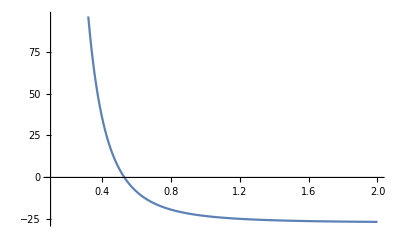

```mathematica
Plot[(4.-27. a^3)/a^3,{a,0.1,2}]
```

```mathematica
N[Discriminant[x^3-x^2/a+1,x]]/.a->1/(1+8/9)
```

-0.042524

```mathematica
r[i_]:=x/.NSolve[x^3-x^2/(1/(1+8/9))+1==0,x][[i]]
```

```mathematica
Table[r[i],{i,3}]
```

{-0.630071,1.25948-0.0288715 ⅈ,1.25948+0.0288715 ⅈ}

```mathematica
N[Discriminant[x^3-x/(1/(1+8/9))+1,x]]
```

-0.042524

```mathematica
s[i_]:=x/.NSolve[x^3-x/(1/(1+8/9))+1==0,x][[i]]
```

```mathematica
Table[s[i],{i,3}]
```

{-1.58712,0.793562-0.0181911 ⅈ,0.793562+0.0181911 ⅈ}

```mathematica
(*parametric six fold rational Pisot cylinder symmetry*)
```

```mathematica
x0={-r[1]*Cos[t],-Abs[r[2]]*Cos[t-Arg[r[2]]],-Abs[r[2]]*Cos[t-Arg[r[3]]]}
```

{0.630071 Cos[t],-1.25981 Cos[0.0229193+t],-1.25981 Cos[0.0229193-t]}

```mathematica
y0={-s[1]*Cos[p+Pi],0+Abs[s[2]]*Cos[p-Arg[r[2]]+Pi],0+Abs[r[2]]*Cos[p-Arg[s[3]+Pi]]}
```

{-1.58712 Cos[p],0.79377 Cos[3.16451+p],1.25981 Cos[0.00462267-p]}

```mathematica
w=FullSimplify[ExpandAll[Table[x0[[i]]*y0[[i]],{i,3}]]]
```

{-1. Cos[p] Cos[t],-1. Cos[3.16451+p] Cos[0.0229193+t],-1.58712 Cos[0.00462267-p] Cos[0.0229193-t]}

```mathematica
ParametricPlot3D[w,{t,-Pi,Pi},{p,-Pi,Pi},Mesh->None,ColorFunction->"Rainbow",ImageSize->Full,PlotPoints->100,PlotRange->All]
```

-Graphics3D-

```mathematica
ParametricPlot3D[w/(w.w),{t,-Pi,Pi},{p,-Pi,Pi},Mesh->None,ColorFunction->"Rainbow",ImageSize->Full,PlotPoints->200,PlotRange->All,ViewPoint->Above]
```

-Graphics3D-

```mathematica
Clear[x,y,z,t,p,r]
```

```mathematica
(* coordinates normalized on unit radius r*)
```

```mathematica
1.5871231010954476/0.9427073627769
```

1.68358

```mathematica
x=-r*w[[1]]/1.5871231010954476
```

0.630071 r Cos[p] Cos[t]

```mathematica
y=-r*w[[2]]/1.5871231010954476
```

0.630071 r Cos[3.16451+p] Cos[0.0229193+t]

```mathematica
z=-r*w[[3]]/1.5871231010954476
```

1. r Cos[0.00462267-p] Cos[0.0229193-t]

```mathematica
(* volume calculation*)
```

```mathematica
xr=D[x,r]
```

0.630071 Cos[p] Cos[t]

```mathematica
yr=D[y,r]
```

0.630071 Cos[3.16451+p] Cos[0.0229193+t]

```mathematica
zr=D[z,r]
```

1. Cos[0.00462267-p] Cos[0.0229193-t]

```mathematica
xt=D[x,t]
```

-0.630071 r Cos[p] Sin[t]

```mathematica
yt=D[y,t]
```

-0.630071 r Cos[3.16451+p] Sin[0.0229193+t]

```mathematica
zt=D[z,t]
```

1. r Cos[0.00462267-p] Sin[0.0229193-t]

```mathematica
xp=D[x,p]
```

-0.630071 r Cos[t] Sin[p]

```mathematica
yp=D[y,p]
```

-0.630071 r Cos[0.0229193+t] Sin[3.16451+p]

```mathematica
zp=D[z,p]
```

1. r Cos[0.0229193-t] Sin[0.00462267-p]

```mathematica
h1=1/Sqrt[xr^2+yr^2+zr^2]
```

1/(√(1. Cos[0.00462267-p]^2 Cos[0.0229193-t]^2+0.396989 Cos[p]^2 Cos[t]^2+0.396989 Cos[3.16451+p]^2 Cos[0.0229193+t]^2))

```mathematica
h2=1/Sqrt[xt^2+yt^2+zt^2]
```

1/(√(1. r^2 Cos[0.00462267-p]^2 Sin[0.0229193-t]^2+0.396989 r^2 Cos[p]^2 Sin[t]^2+0.396989 r^2 Cos[3.16451+p]^2 Sin[0.0229193+t]^2))

```mathematica
h3=1/Sqrt[xp^2+yp^2+zp^2]
```

1/(√(1. r^2 Cos[0.0229193-t]^2 Sin[0.00462267-p]^2+0.396989 r^2 Cos[t]^2 Sin[p]^2+0.396989 r^2 Cos[0.0229193+t]^2 Sin[3.16451+p]^2))

```mathematica
Clear[r]
```

```mathematica
dr2=1/h1^2
```

1. Cos[0.00462267-p]^2 Cos[0.0229193-t]^2+0.396989 Cos[p]^2 Cos[t]^2+0.396989 Cos[3.16451+p]^2 Cos[0.0229193+t]^2

```mathematica
dt2=1/h2^2
```

1. r^2 Cos[0.00462267-p]^2 Sin[0.0229193-t]^2+0.396989 r^2 Cos[p]^2 Sin[t]^2+0.396989 r^2 Cos[3.16451+p]^2 Sin[0.0229193+t]^2

```mathematica
dp2=1/h3^2
```

1. r^2 Cos[0.0229193-t]^2 Sin[0.00462267-p]^2+0.396989 r^2 Cos[t]^2 Sin[p]^2+0.396989 r^2 Cos[0.0229193+t]^2 Sin[3.16451+p]^2

```mathematica
(* implicit function on {r,t,p} coordinates*)
```

```mathematica
ds2=dr2/h1^2+dt2/h2^2+dp2/h3^2
```

(1. Cos[0.00462267-p]^2 Cos[0.0229193-t]^2+0.396989 Cos[p]^2 Cos[t]^2+0.396989 Cos[3.16451+p]^2 Cos[0.0229193+t]^2)^2+(1. r^2 Cos[0.0229193-t]^2 Sin[0.00462267-p]^2+0.396989 r^2 Cos[t]^2 Sin[p]^2+0.396989 r^2 Cos[0.0229193+t]^2 Sin[3.16451+p]^2)^2+(1. r^2 Cos[0.00462267-p]^2 Sin[0.0229193-t]^2+0.396989 r^2 Cos[p]^2 Sin[t]^2+0.396989 r^2 Cos[3.16451+p]^2 Sin[0.0229193+t]^2)^2

```mathematica
(* volume element*)
```

```mathematica
dv=1/(h1*h2*h3)
```

√(1. Cos[0.00462267-p]^2 Cos[0.0229193-t]^2+0.396989 Cos[p]^2 Cos[t]^2+0.396989 Cos[3.16451+p]^2 Cos[0.0229193+t]^2) √(1. r^2 Cos[0.0229193-t]^2 Sin[0.00462267-p]^2+0.396989 r^2 Cos[t]^2 Sin[p]^2+0.396989 r^2 Cos[0.0229193+t]^2 Sin[3.16451+p]^2) √(1. r^2 Cos[0.00462267-p]^2 Sin[0.0229193-t]^2+0.396989 r^2 Cos[p]^2 Sin[t]^2+0.396989 r^2 Cos[3.16451+p]^2 Sin[0.0229193+t]^2)

```mathematica
(*three fold volume integration*)
```

```mathematica
A=Integrate[dv,{r,0,1}]
```

1/3 √(1. Cos[0.00462267-p]^2 Cos[0.0229193-t]^2+0.396989 Cos[p]^2 Cos[t]^2+0.396989 Cos[3.16451+p]^2 Cos[0.0229193+t]^2) √(1. Cos[0.0229193-t]^2 Sin[0.00462267-p]^2+0.396989 Cos[t]^2 Sin[p]^2+0.396989 Cos[0.0229193+t]^2 Sin[3.16451+p]^2) √(1. Cos[0.00462267-p]^2 Sin[0.0229193-t]^2+0.396989 Cos[p]^2 Sin[t]^2+0.396989 Cos[3.16451+p]^2 Sin[0.0229193+t]^2)

```mathematica
B=NIntegrate[A,{t,0,Pi}]
```

NIntegrate::inumr: The integrand 1/3 √(1. Cos[«21»+«1»]^2 Cos[0.0229193+Times[«1»]]^2+«1»+0.396989 («1»)^2 («1»)^2) √(«1») √(1. Cos[0.00462267+Times[«2»]]^2 Sin[0.0229193+Times[«2»]]^2+0.396989 Cos[p]^2 Sin[t]^2+0.396989 Cos[3.16451+p]^2 Sin[0.0229193+t]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159}}.

NIntegrate[A,{t,0,π}]

```mathematica
C1=NIntegrate[B,{p,0,Pi}]
```

NIntegrate::inumr: The integrand 1/3 √(1. Cos[«21»+«1»]^2 Cos[0.0229193+Times[«1»]]^2+«1»+0.396989 («1»)^2 («1»)^2) √(«1») √(1. Cos[0.00462267+Times[«2»]]^2 Sin[0.0229193+Times[«2»]]^2+0.396989 Cos[p]^2 Sin[t]^2+0.396989 Cos[3.16451+p]^2 Sin[0.0229193+t]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.357236

```mathematica
(* volume from calculation*)
```

```mathematica
N[C1,20]
```

0.357236

```mathematica
(* divided by the weeks volume*)
```

```mathematica
N[C1/0.9427073627769,20]
```

```mathematica
0.378947123298773/0.05644637167371669
```

```mathematica
6.713400915992328/(4+Exp[1])
```

0.999273

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
(*rational cubic Pisot*)
```

```mathematica
Clear[x]
```

```mathematica
w0=x/.NSolve[x^3-x/(1/(1+8/9))-1==0,x]
```

{-0.793562-0.0181911 ⅈ,-0.793562+0.0181911 ⅈ,1.58712}

```mathematica
Abs[w0]
```

{0.79377,0.79377,1.58712}

```mathematica
(*Weirstrass elliptc function:w^2=4*x^3-4x/a-4*)
```

```mathematica
g2=4/(1/(1+8/9));g3=4;
```

```mathematica
j=g2^3/(g2^3-27*g3^2)
```

-19652/31

```mathematica
N[Discriminant[x^3-x/(1/(1+8/9))-1,x]]
```

-0.042524

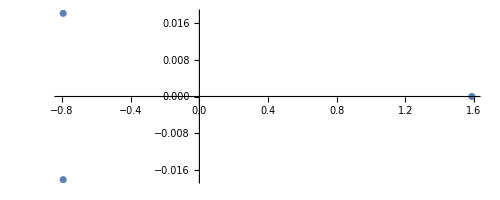

```mathematica
ComplexListPlot[w0,AspectRatio->Automatic]
```

```mathematica
Clear[a]
```

```mathematica
(* cubic recursion function*)
```

```mathematica
a[0]=1;a[1]=1;a[2]=1;
a[n_]:=a[n]=a[n-2]/(1/(1+8/9))+a[n-3]
```

```mathematica
(* using powers of three to make an integer sequence:*)
```

```mathematica
w=Table[(3)^n*a[n],{n,0,20}]
```

{1,3,9,78,234,1569,6084,32991,145791,725115,3369204,16263312,76854573,367444812,1745637165,8321635275,39596841729,188600003130,897830461818,4275314779893,20355317935416}

```mathematica
(* OEIS: Search:seq:1,3,9,78,234,1569,6084,32991,145791,725115

Sorry,but the terms do not match anything in the table.*)
```

```mathematica
(* Sequence function exists*)
```

```mathematica
f[n_]=FindSequenceFunction[w,n]
```

(Root4.76Root[-27-17 #1+#1^3&,1]4.761369303286343)^n Root0.119Root[-2601+21777 #1+248 #1^2+837 #1^3&,1]0.11921098471573778+(Root-2.38-0.0546 ⅈRoot[-27-17 #1+#1^3&,2]-2.3806846516431714)^n Root-0.208-5.10 ⅈRoot[-2601+21777 #1+248 #1^2+837 #1^3&,2]-0.20775364050601702+(Root-2.38+0.0546 ⅈRoot[-27-17 #1+#1^3&,3]-2.3806846516431714)^n Root-0.208+5.10 ⅈRoot[-2601+21777 #1+248 #1^2+837 #1^3&,3]-0.20775364050601702

```mathematica
Table[FullSimplify[f[n]],{n,20}]
```

{1,3,9,78,234,1569,6084,32991,145791,725115,3369204,16263312,76854573,367444812,1745637165,8321635275,39596841729,188600003130,897830461818,4275314779893}

```mathematica
(* generating function exists*)
```

```mathematica
g[x_]=FindGeneratingFunction[w,x]
```

(-1-3 x+8 x^2)/(-1+17 x^2+27 x^3)

```mathematica
CoefficientList[Normal[Series[g[x],{x,0,100}]],x]
```

{1,3,9,78,234,1569,6084,32991,145791,725115,3369204,16263312,76854573,367444812,1745637165,8321635275,39596841729,188600003130,897830461818,4275314779893,20355317935416,96921773727267,461473903959183,2197263737619771,10461944257942320,49813278946434048,237179173300753257,1129298237053821456,5377004477666524665,25601907709035302691,121900128520784098617,580411551950596311702,2763553692997282849146,13158299853221307961593,62651524683619908851436,298307047215688872274023,1420350015658513765437423,6762810969124448367647163,32200240541018333563834812,153317236897895493916812192,729999985363671776511665205,3475799521871718402809347188,16549565147425598536452237669,78798591476638350813573862731,375189194596771571995540414449,1786414314083343124314966083490,8505778278014352195890681339370,40499151593529665557234014609453,192831417206494251686645667023520,918141590596391823762026644523691,4371611185535703248718294733855071,20814855304714005799493885966537787,99107213100209534469785729877675864,471886042189602086306790019245229296,2246823715930840242572692329017009937,10697957470928892897899645033866146360,50936926309943540454019100112910359921,242529517335923865813756658459183756419,1154772598984120295961615117833862070377,5498298805079181311092378896854703576990,26179431150799989408318886781573616619722,124649939858917330279534049428044236709009,593504397300737715340915305501828479114004,2825893618673194328776688783379239672785647,13455123130303309078342979528088278536081311,64064810244564221903408422565996443373434107,305036220919332501208801249128740206278594756,1452390098675781117473203630880323057822575216,6915365632231886511941648644470487477818831741,32926609642310256529682095451441477552505837084,156775748412188160874784524989767009684129670429,746467235989535296827020136075208280293707687435,3554206183349575661172753502014959058547861998561,16922888218951180389678524488002250026464531787978,80576120488660239254266353208284927563243761536282,383652666672608609476199260850442145030689314356773,1826712030218905937843848165716904519289686304392200,8697650586628172820960578971081209509729299905544755,41412726513881833399202798860149314743753278662300271,197181284788589398278113742982736983686219628612850235,938852916574951833952383212841731007406496834708812992,4470225457280829272506409199930560220747072210300561312,21284394271066094930699585678843325685438376162596777209,101342861521297797149323303145546260952675642112247493088,482530789954706004179566004938461662612623344442260367977,2297507291180847114667384966803056229702322072298320367139,10939280690305042594084351268883597310136839192549108568985,52085955278851463062193826568990420795480305529012476176742,248000468597068596195453365674703672474288962225389495585498,1180821818378711022097572535932694280896859852192038026367209,5622328758679155638001940533832703793540880607114958281725500,26769983564558939472935973984072801932052419467350162829050999,127461777993770843442667447545338710074410186330139317501248143,606892597081839173265963952142720635270494907337056641700455483,2889639782137195704294617905840723723430388493230822793905595404,13758642156223078718473408270150395971607488455643724481441443072,65509976417541984651189531107145760450619966883024516822307419909,311917190773496622230002624050256272049947793063175531619955608132,1485152937316236864469004052115538618893941625313797346978145101397,7071361606423076163492161948747292157015851587915645991741545675787,33669364085260435496183139735321075866545598043040294252367268143313}

```mathematica
Table[N[w[[n+1]]/w[[n]]],{n,Length[w]-1}]
```

{3.,3.,8.66667,3.,6.70513,3.87763,5.42258,4.41911,4.97366,4.64644,4.82705,4.72564,4.78104,4.75075,4.7671,4.7583,4.76301,4.7605,4.76183,4.76113}

```mathematica
%/1.5871231010954472
```

{1.89021,1.89021,5.46061,1.89021,4.22471,2.44318,3.41661,2.78436,3.13376,2.92759,3.04138,2.97749,3.01239,2.99331,3.00361,2.99807,3.00103,2.99945,3.00029,2.99985}

```mathematica
Table[3*a[n+1]/(a[n]),{n,0,10}]
```

{3,3,26/3,3,523/78,2028/523,10997/2028,48597/10997,241705/48597,1123068/241705,1355276/280767}

```mathematica
Table[N[a[n+1]/a[n]],{n,0,100}]
```

{1.,1.,2.88889,1.,2.23504,1.29254,1.80753,1.47304,1.65789,1.54881,1.60902,1.57521,1.59368,1.58358,1.58903,1.5861,1.58767,1.58683,1.58728,1.58704,1.58717,1.5871,1.58713,1.58712,1.58713,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712,1.58712}

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
Clear[cr,cols,cr2,cr3,cr4,firstCols]
allColors=ColorData["Legacy"][[3,1]];
firstCols={"White","AliceBlue","LightBlue" ,"Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
cr2[n_]:=cr2[n]=cols[[n+4]];
```

```mathematica
cr3[n_]:=cr3[n]=cols[[n+8]];
```

```mathematica
cr4[n_]:=cr4[n]=cols[[n+12]];
```

```mathematica
cr5[n_]:=cr5[n]=cols[[n+16]]
```

```mathematica
Clear[w,ww,n,m,a0,a,b,A,B,c0,b0]
```

```mathematica
Clear[f1,f2,f3,m,z,s]
(*rational cubic*)
r[i_]:=x/.NSolve[x^3-x^2/(1/(1+8/9))+1==0,x][[i]]
mu=2.0
s[1]=N[{{1+I,mu*r[1]},{1/(mu*r[1]),1-I}}]
s[2]=N[{{1,0},{mu*r[2],1}}]
s[3]=N[{{1,0},{mu*r[3],1}}]
s[4]=N[{{1,0},{0,1}}]
Table[Det[s[i]],{i,4}]
Table[Tr[s[i]],{i,4}]
```

2.

{{1.+1. ⅈ,-1.26014},{-0.793562,1.-1. ⅈ}}

{{1.,0.},{2.51896-0.0577429 ⅈ,1.}}

{{1.,0.},{2.51896+0.0577429 ⅈ,1.}}

{{1.,0.},{0.,1.}}

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.}

{2.+0. ⅈ,2.,2.,2.}

```mathematica
s0=N[{{1,-I},{-I,1}}/Sqrt[2]];s1=Inverse[s0];
qf=N[rotate[Pi/8]];qfi=Inverse[qf];
```

```mathematica
{a,b,A,B}=Table[N[s[i]],{i,4}]
```

{{{1.+1. ⅈ,-1.26014},{-0.793562,1.-1. ⅈ}},{{1.,0.},{2.51896-0.0577429 ⅈ,1.}},{{1.,0.},{2.51896+0.0577429 ⅈ,1.}},{{1.,0.},{0.,1.}}}

```mathematica
Det[a]
Tr[a]
Det[b]
Tr[b]
Det[A]
Tr[A]
Det[B]
Tr[B]
```

1.+0. ⅈ

2.+0. ⅈ

1.+0. ⅈ

2.

1.+0. ⅈ

2.

1.

2.

```mathematica
Affine[{z1_,z2_}]:=0.00001 Round[(z1/z2)/0.00001];
Children[{z_,n_}]:={Affine[{a,b,A,B}[[#]].{Conjugate[z],1}],#}&/@Delete[Range[4],{3,4,1,2}[[n]]];
aa1={Re[#[[1]]],Im[#[[1]]]}&/@Nest[Union[Flatten[Children/@#,1]]&,ParallelTable[{Affine[{a,b,A,B}[[i]].{0,1}],i},{i,1,4}],15];
ll=Length[aa1]
```

1127726

```mathematica
Last[aa1]
```

{6.26307,1.06993}

```mathematica
aa=Delete[Union[aa1],Length[Union[aa1]]];
```

```mathematica
g0=Rasterize[ListPlot[aa,AspectRatio->Automatic,ColorFunction->"CMYKColors",PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->{{-8,8},{-8,8}}*2/8],RasterSize->2000,ImageSize->2000];
```

```mathematica
dlst=ParallelTable[Mod[1+Floor[1+(1+Floor[24*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst]
Max[dlst]
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
g2=Graphics[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->2000,Background->Black,PlotRange->{{-8,8},{-8,8}}*(2/8)];
```

2

151

```mathematica
Export["Nylander_3group_Rational_Needle_scaled_Limitset_15.jpg",{g0,g2}]
(*end*)
```

Lookup::invrl: The argument Missing[NotAvailable] is not a valid Association or a list of rules.